### Task 1.4.

Finding Curvature:

```mathematica
f[x_]=x^3;
k[x_]=Abs[f''[x]]/((1+(f'[x])^2)^(3/2));
k[x]
```

(6 Abs[x])/((1+9 x^4)^(3/2))

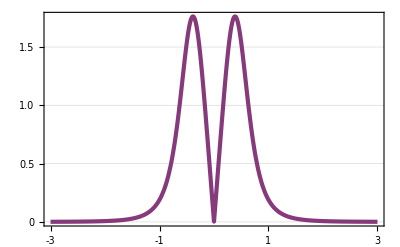

```mathematica
Plot[k[x],{x,-3,3},ColorFunction->"Rainbow",PlotTheme->"Business"]
```

### Task 2.

```mathematica
a=2.0;
x[t_]=a/Cosh[t];
y[t_]=a(t+Tanh[t]);
Show[
ParametricPlot[{x[t],y[t]},{t,-5,5},PlotTheme->"Business",AspectRatio->1/GoldenRatio],
ListPlot[{{x[1/2 ArcCosh[5]],y[1/2 ArcCosh[5]]},{x[-1/2 ArcCosh[5]],y[-1/2 ArcCosh[5]]},{x[0],y[0]}}->{"Zero Curvature","Zero Curvature","Local maxima"},PlotStyle->{Red,PointSize[0.015]}],ImageSize->500
]
```

-Graphics-

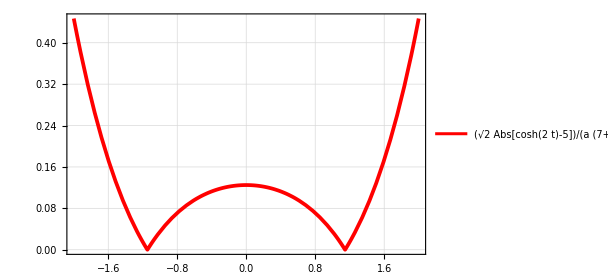

```mathematica
Plot[Sqrt[2]/a Abs[Cosh[2t]-5]/(7+Cosh[t])^(3/2),{t,-2,2},PlotStyle->{Red,Thickness[0.006]},PlotTheme->"Detailed",ImageSize->450]
```

```mathematica
Solve[Sqrt[2]/2 Abs[Cosh[2x]-5]/(7+Cosh[x])^(3/2)==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-ArcCosh[5]/2},{x→ArcCosh[5]/2}}

### Task 3.

Curve Plot

```mathematica
Clear[x,y,z,b,c,α]
x[t_,b_]=c Cos[b t]+r Cos[α t]Cos[b t];
y[t_,b_]=c Sin[b t]+r Cos[α t]Sin[b t];
z[t_]=r Sin[α t];
c=2.0;r=8.0;α=5.0;
plots=Table[ParametricPlot3D[{x[t,b],y[t,b],z[t]},{t,-100,100},ColorFunction->"Rainbow",PlotTheme->"Business"],{b,1,10}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Projections on x,y,z axes

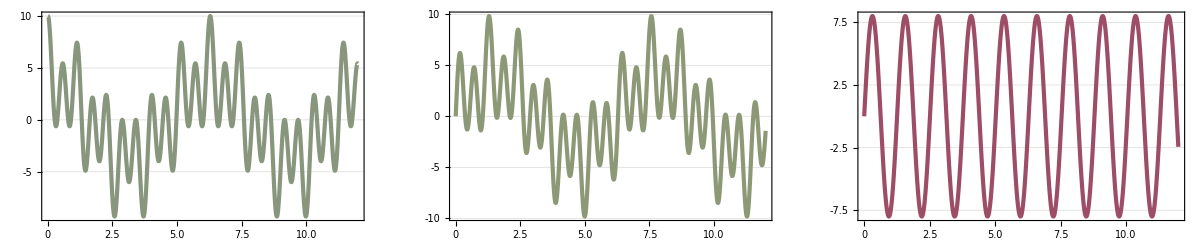

```mathematica
px=Plot[x[t,6.0],{t,0,12},ColorFunction->"Rainbow",PlotTheme->"Business"];
py=Plot[y[t,6.0],{t,0,12},ColorFunction->"Rainbow",PlotTheme->"Business"];
pz=Plot[z[t],{t,0,12},ColorFunction->"Rainbow",PlotTheme->"Business"];
GraphicsRow[{px,py,pz}]
```

First Derivative

```mathematica
Remove[c,r,α,β];
x[t_]=(r Cos[α t])Cos[β t];
y[t_]=(r Cos[α t])Sin[β t];
z[t_]=r Sin[α t];
f={x[t],y[t],z[t]};
x1[t_]=Simplify[D[x[t],t]];
y1[t_]=Simplify[D[y[t],t]];
z1[t_]=Simplify[D[z[t],t]];
f1={x1[t],y1[t],z1[t]};
Print["Derivative is ",f1]
```

Derivative is {-r (α Cos[t β] Sin[t α]+β Cos[t α] Sin[t β]),r (β Cos[t α] Cos[t β]-α Sin[t α] Sin[t β]),r α Cos[t α]}

```mathematica
l[t_]=Simplify[(x1[t])^2+(y1[t])^2+(z1[t])^2];
Print["Square of length is ",l[t]]
```

Square of length is 1/2 r^2 (2 α^2+β^2+β^2 Cos[2 t α])

Natural Parameter

```mathematica
Clear[k]
Simplify[Integrate[Sqrt[l[t]],t],r>0&&α>0&&β>0]
```

(r √(α^2+β^2) EllipticE[t α,β^2/(α^2+β^2)])/α

Second Derivative

```mathematica
x2[t_]=Simplify[D[x1[t],t]];
y2[t_]=Simplify[D[y1[t],t]];
z2[t_]=Simplify[D[z1[t],t]];
f2=Simplify[{x2[t],y2[t],z2[t]}];
Print["Second derivative is ",f2]
```

Second derivative is {-r (α^2+β^2) Cos[t α] Cos[t β]+2 r α β Sin[t α] Sin[t β],-r (2 α β Cos[t β] Sin[t α]+(α^2+β^2) Cos[t α] Sin[t β]),-r α^2 Sin[t α]}

Cross Product (aka binormal)

```mathematica
f1f2=Simplify[Cross[f1,f2]];
Print["Cross product is ",f1f2]
```

Cross product is {r^2 α (α β Cos[t α] Cos[t β] Sin[t α]+(α^2+β^2) Cos[t α]^2 Sin[t β]+α^2 Sin[t α]^2 Sin[t β]),-r^2 α ((α^2+β^2) Cos[t α]^2 Cos[t β]+α^2 Cos[t β] Sin[t α]^2-1/2 α β Sin[2 t α] Sin[t β]),1/2 r^2 β (3 α^2+β^2+(-α^2+β^2) Cos[2 t α])}

```mathematica
cross1=Simplify[f1f2[[1]]];
cross2=Simplify[f1f2[[2]]];
cross3=Simplify[f1f2[[3]]];
Print["First component: ",cross1];
Print["Second component: ",cross2];
Print["Third component: ",cross3];
```

First component: r^2 α (α β Cos[t α] Cos[t β] Sin[t α]+(α^2+β^2) Cos[t α]^2 Sin[t β]+α^2 Sin[t α]^2 Sin[t β])

Second component: -r^2 α ((α^2+β^2) Cos[t α]^2 Cos[t β]+α^2 Cos[t β] Sin[t α]^2-1/2 α β Sin[2 t α] Sin[t β])

Third component: 1/2 r^2 β (3 α^2+β^2+(-α^2+β^2) Cos[2 t α])

Cross product vector length

```mathematica
crossL=Simplify[Sqrt[cross1^2+cross2^2+cross3^2],r>0&&α>0&&β>0];
Print["Length of cross product is ",crossL]
```

Length of cross product is (r^2 √(8 α^6+28 α^4 β^2+13 α^2 β^4+3 β^6+4 β^2 (-α^4+3 α^2 β^2+β^4) Cos[2 t α]+(-α^2 β^4+β^6) Cos[4 t α]))/(2 √2)

```mathematica
simplifiedL=Simplify[r^2/(2Sqrt[2])Sqrt[8 α^6+28 α^4 β^2+13 α^2 β^4+3 β^6+4 β^2 (-α^4+3 α^2 β^2+β^4) Cos[2 t α]+(-α^2 β^4+β^6) Cos[4 t α]]/.{β->α},α>0&&r>0]
Solve[simplifiedL==0,t]
```

(r^2 α^3 √(13+3 Cos[2 t α]))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-ArcCos[-13/3]/(2 α)},{t→ArcCos[-13/3]/(2 α)}}

Curvature

```mathematica
curvature=Simplify[crossL/Sqrt[l[t]],α>0&&β>0&&r>0]
```

(r √(8 α^6+28 α^4 β^2+13 α^2 β^4+3 β^6+4 β^2 (-α^4+3 α^2 β^2+β^4) Cos[2 t α]+(-α^2 β^4+β^6) Cos[4 t α]))/(2 √(2 α^2+β^2+β^2 Cos[2 t α]))

```mathematica
simplifiedCurvature=Simplify[simplifiedL/((l[t])^(3/2)/.{β->α}),α>0&&r>0]
```

(2 √(13+3 Cos[2 t α]))/(r (3+Cos[2 t α])^(3/2))

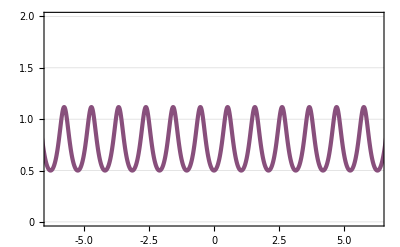

```mathematica
Plot[simplifiedCurvature/.{α->3.0,r->2.0},{t,-10,10},PlotRange->{{-2π,2π},{0,2}},ColorFunction->"Rainbow",PlotTheme->"Business"]
```

Torsion

```mathematica
x3[t_]=Simplify[D[x2[t],t]];
y3[t_]=Simplify[D[y2[t],t]];
z3[t_]=Simplify[D[z2[t],t]];
f3=Simplify[{x3[t],y3[t],z3[t]}]
Needs["VectorAnalysis`"];
triplet=Simplify[Det[{f1,f2,f3}]]
```

{r (α (α^2+3 β^2) Cos[t β] Sin[t α]+β (3 α^2+β^2) Cos[t α] Sin[t β]),r (-β (3 α^2+β^2) Cos[t α] Cos[t β]+α (α^2+3 β^2) Sin[t α] Sin[t β]),-r α^3 Cos[t α]}

General::obspkg: VectorAnalysis` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

1/2 r^3 α β Cos[t α] (4 α^4+7 α^2 β^2+β^4+(-α^2 β^2+β^4) Cos[2 t α])

```mathematica
SimplifiedTriplet=triplet/.{β->α}
```

6 r^3 α^6 Cos[t α]

```mathematica
torsion=Simplify[SimplifiedTriplet/simplifiedCurvature^2]
```

(3 r^5 α^6 Cos[t α] (3+Cos[2 t α])^3)/(26+6 Cos[2 t α])

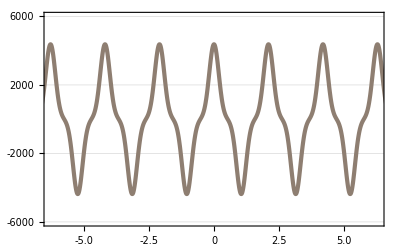

```mathematica
Plot[torsion/.{α->3.0,r->1.0},{t,-10,10},PlotRange->{{-2π,2π},{-6000,6000}},ColorFunction->"Rainbow",PlotTheme->"Business"]
```

```mathematica
xTorsion[t_]=x[t]/.{α->5.0,β->5.0,r->2.0};
yTorsion[t_]=y[t]/.{α->5.0,β->5.0,r->2.0};
zTorsion[t_]=z[t]/.{α->5.0,β->5.0,r->2.0};
u=Table[{xTorsion[π/(2 5.0)+π/5.0 k],yTorsion[π/(2 5.0)+π/5.0 k],zTorsion[π/(2 5.0)+π/5.0 k]},{k,2}];
Show[
ParametricPlot3D[{xTorsion[t],yTorsion[t],zTorsion[t]},{t,-100,100},ColorFunction->"Rainbow",PlotTheme->"Business"],
ListPointPlot3D[u->{"Zero Torsion","Zero Torsion"},PlotStyle->{Green,PointSize[0.04]}]
]
```

-Graphics3D-

```mathematica
X[t_]=3.0 Cos[5 t]Cos[8 t];
Y[t_]=3.0Cos[5 t]Sin[8 t];
Z[t_]=3.0 Sin[5 t];
u=Table[{X[π/(2 5.0)+π/5.0 k],Y[π/(2 5.0)+π/5.0 k],Z[π/(2 5.0)+π/5.0 k]},{k,2}];
```

```mathematica
Show[
ParametricPlot3D[{X[t],Y[t],Z[t]},{t,-100,100},ColorFunction->"Rainbow",PlotTheme->"Business"],
ListPointPlot3D[u->{"Zero Torsion","Zero Torsion"},PlotStyle->{Green,PointSize[0.04]}]
]
```

-Graphics3D-

### Task 5.

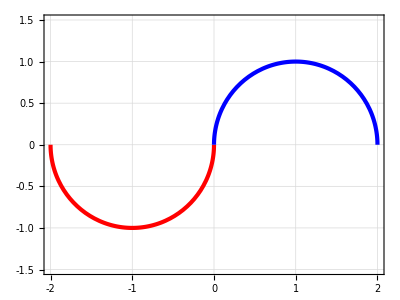

```mathematica
x1[t_]=-1-Cos[t];
x2[t_]=1+Cos[t];
y[t_]=-Sin[t];
Show[
ParametricPlot[{x1[t],y[t]},{t,0,π},PlotTheme->"Business",PlotStyle->Red],
ParametricPlot[{x2[t],y[t]},{t,π,2π},PlotTheme->"Business",PlotStyle->Blue],
PlotRange->{{-2,2},{-1.5,1.5}}
]
```

```mathematica
Clear[t]
Subscript[ϕ, 1]=-π/4;Subscript[ϕ, 2]=+π/4;
Subscript[R, 1] = {{Cos[Subscript[ϕ, 1]],0,-Sin[Subscript[ϕ, 1]]},{0,1,0},{Sin[Subscript[ϕ, 1]],0,Cos[Subscript[ϕ, 1]]}};
Subscript[R, 2] = {{Cos[Subscript[ϕ, 2]],0,-Sin[Subscript[ϕ, 2]]},{0,1,0},{Sin[Subscript[ϕ, 2]],0,Cos[Subscript[ϕ, 2]]}};
plane1 =Subscript[R, 1].{0,0,1};
plane2 =Subscript[R, 2].{0,0,1};
f1R[t_]=Simplify[Subscript[R, 1].{x1[t],y[t],0}];
f2R[t_]=Simplify[Subscript[R, 2].{x2[t],y[t],0}];
Print["Equation for the first part of a function: f_1(t)=",f1R[t]]
Print["Equation for the second part of a function: f_2(t)=",f2R[t]]
Show[
ParametricPlot3D[f1R[t],{t,0,π},PlotTheme->"Business",PlotStyle->Red],
ParametricPlot3D[f2R[t],{t,π,2π},PlotTheme->"Business",PlotStyle->Blue],
ContourPlot3D[plane1.{x,y,z}==0,{x,-1.5,1.5},{y,-1.5,1.5},{z,0,2},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.8],Specularity[White,30]]],
ContourPlot3D[plane2.{x,y,z}==0,{x,-1.5,1.5},{y,-1.5,1.5},{z,0,2},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.8],Specularity[White,30]]],
PlotRange->{{-1.5,1.5},{-1.5,1.5},{0,2}}
]
```

Equation for the first part of a function: f_1(t)={-(1+Cos[t])/(√2),-Sin[t],(1+Cos[t])/(√2)}

Equation for the second part of a function: f_2(t)={(1+Cos[t])/(√2),-Sin[t],(1+Cos[t])/(√2)}

-Graphics3D-

```mathematica
fR[t_]={(1+Cos[t])/Sqrt[2] Sign[t-π],-Sin[t],(1+Cos[t])/Sqrt[2]};
fdotR[t_]={-Sin[t]/Sqrt[2] Sign[t-π],-Cos[t],-Sin[t]/Sqrt[2]};
Animate[
Show
[
ParametricPlot3D[fR[t],{t,0,2π},PlotTheme->"Business",PlotStyle->Black],
Graphics3D[{Red,Thickness[0.01],Arrowheads[0.05],Arrow[{fR[τ],fR[τ]+fdotR[τ]}]}],
PlotRange->{{-2,2},{-2,2},{-1,2}}
],
{τ,0,2π}
]
```

```mathematica
fddotR[t_]={-Cos[t]/Sqrt[2] Sign[t-π],Sin[t],-Cos[t]/Sqrt[2]};
β[t_]=Simplify[Cross[fdotR[t],fddotR[t]]]
```

{1/(√2),0,Sign[π-t]/(√2)}

```mathematica
ν[t_]=Simplify[Cross[β[t],fdotR[t]]]
```

{(Cos[t] Sign[π-t])/(√2),1/2 (1+Sign[π-t]^2) Sin[t],-Cos[t]/(√2)}

```mathematica
Animate[
Show
[
ParametricPlot3D[fR[t],{t,0,2π},PlotTheme->"Business",PlotStyle->Black],
Graphics3D[{Red,Thickness[0.01],Arrowheads[0.05],Arrow[{fR[τ],fR[τ]+fdotR[τ]}]}],
Graphics3D[{Blue,Thickness[0.01],Arrowheads[0.05],Arrow[{fR[τ],fR[τ]+β[τ]}]}],Graphics3D[{Green,Thickness[0.01],Arrowheads[0.05],Arrow[{fR[τ],fR[τ]+ν[τ]}]}],
PlotRange->{{-2,2},{-2,2},{-1,2}}
],
{τ,0,2π}
]
```

Curvature and Torsion

```mathematica
fdddotR[t_]={Sin[t]/Sqrt[2] Sign[t-π],Cos[t],Sin[t]/Sqrt[2]};
tripletProd=Simplify[Det[{fdotR[t],fddotR[t],fdddotR[t]}]]
```

0